# 1-D universal estimator using DNN with range adjustment

Given the pdf of some distribution and a sample containing m observations drawn from dist using pdf with true parameter θ, The UniversalEstimator(pdf, sample, θ) returns  a tuple (Overscript[θ, ^], e, CRB) where Overscript[θ, ^] is the predicted parameter, e is the abs-error | θ - Overscript[θ, ^] | and CRB is the Cramer-Rao-Bound (θ, m) of the distribution with θ. We are to explore whether performing range adjustment can have a lower variance for single parameter θ.

## Parameter range adjustment

For convenience, we want to work with parameters  ∈ (0,1) and map them to the parameters in the original range.
For that, we can use the Logistic function and its Logit inverse.

#### The Logistic function

The standard Logistic function, σ(x), defined in (-∞, ∞) and yields values in (0,1):

```mathematica
Sigmoid[x_]:=1/(1+ⅇ^-x)
```

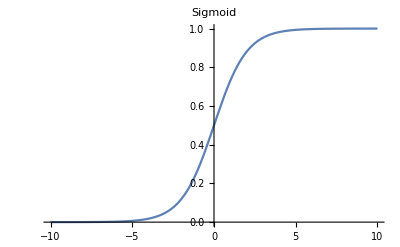

```mathematica
Plot[Sigmoid[x], {x, -10, 10}, PlotLabel->HoldForm[Sigmoid]]
```

#### The Logit function

The Logit  is the inverse of the Logistic function σ(x), defined in (0,1) and yields values in (-∞, ∞).

```mathematica
Logit[x_]:= Log[x/(1-x)]
```

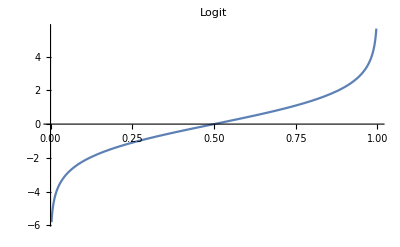

```mathematica
Plot[Logit[x], {x, 0, 1}, PlotLabel->HoldForm[Logit]]
```

### Range Adjuster

```mathematica
Adjuster[low_, high_]:=With[{LOW=Sigmoid[low],HIGH=Sigmoid[high]}, Function[{t},Logit[LOW+t(HIGH-LOW)]]]
```

### Examples

```mathematica
N[Adjuster[1,10][0]]
```

1.

```mathematica
N[Adjuster[1,10][1]]
```

10.

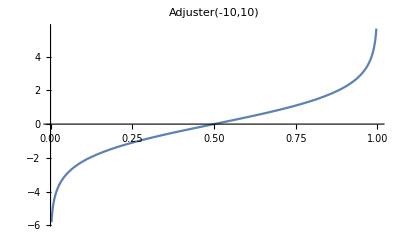

```mathematica
Plot[Adjuster[-10,10][x], {x, 0, 1}, PlotLabel->HoldForm[Adjuster[-10,10]]]
```

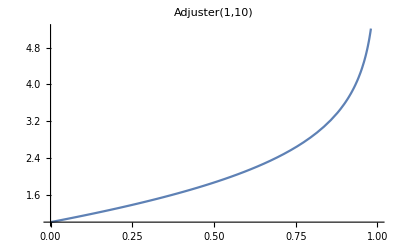

```mathematica
Plot[Adjuster[1,10][x], {x, 0, 1}, PlotLabel->HoldForm[Adjuster[1,10]]]
```

So using this range adjuster only helps to centralize the data of the given range to be more closer to the value which is close to 0

Therefore, I use a new range adjuster with a new mapping function:

#### New-Logistic function:

The New-Logistic function, σ(x), also defined in (-∞, ∞) and yields values in (0, 1) , but the its central shifts to x=a:

```mathematica
NewSigmoid[x_,a_]:=1/(1+ⅇ^(-x+a))
```

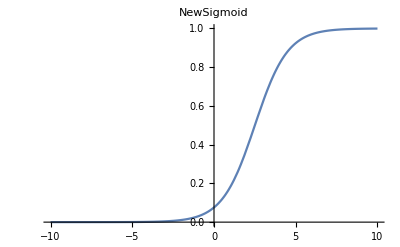

```mathematica
Plot[NewSigmoid[x,2.5], {x, -10, 10}, PlotLabel->HoldForm[NewSigmoid]]
```

#### New - Logit function

```mathematica
NewLogit[x_,a_]:= Log[x/(1-x)]+a
```

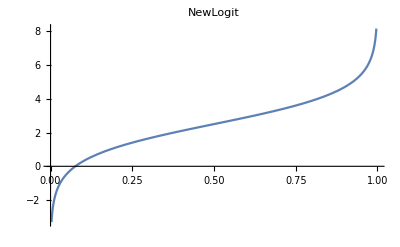

```mathematica
Plot[NewLogit[x,2.5], {x, 0, 1}, PlotLabel->HoldForm[NewLogit]]
```

#### New Range Adjuster

```mathematica
NewAdjuster[low_, high_,a_]:=With[{LOW=NewSigmoid[low,a],HIGH=NewSigmoid[high,a]}, Function[{t},NewLogit[LOW+t(HIGH-LOW),a]]]
```

Given a single parameter a=5 we want to centralize:

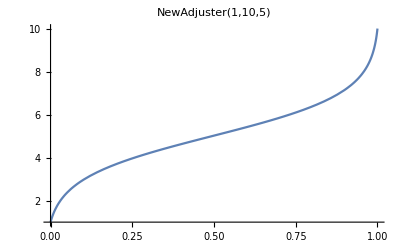

```mathematica
Plot[NewAdjuster[1,10,5][x], {x, 0, 1}, PlotLabel->HoldForm[NewAdjuster[1,10,5]]]
```

### Fisher Information

Fisher information for a distribution with a single parameter θ

```mathematica
FisherInformation[dist_]:=Module[{f},
(*let f be the PDF of dist with parameter θ evaluated at x*)
f = PDF[dist[θ],x];
Expectation[D[Log[f], {θ}]^2,x\[Distributed]dist[θ]]  (*the return of this function*)
]
```

### Cramer-Rao bound

Cramer-Rao bound for a single parameter d and m observations

```mathematica
CRB[dist_, d_, m_]:=(
fi=FisherInformation[dist];
FI[θ_]:=Evaluate[fi];
(1/FI[d])/m  (*the return of this function*)
)
```

## Generating data (without duplicating θ and logging the histogram)

```mathematica
GenerateData[M_, n_, f_, range_, a_, bins_:-1]:=
	Module[{params, samples, nbins, MAXBINS,adjuster},
		(*generate an adjuster for the parameter range*)
		adjuster=NewAdjuster[range[[1]],range[[2]],a];
		(*generate M random parameters in the range [0,1] and adjust them to the original range which will be more central*)
		params=Table[adjuster[RandomReal[{0,1}]],{i,1,M}];
		(*generate M distributions, each distribution has n number/data*, now we have M*n data*)
		samples=Table[f[params[[i]],n],{i,1,M}];
		MAXBINS=2000;
		nbins=If[bins>0,bins,Min[MAXBINS, Ceiling[Max[samples]]+1](*Ceiling[Max[samples]]+2] if using zero padding*)];
		h[x_]:=HistogramList[x,{0,nbins,1}][[2]]; (*without using log10(x+1)*)
		Table[h@samples[[i]]->params[[i]], {i,1,M}]  
	
	]
```

## Example of generated data

```mathematica
(*f[å_,N_]:=RandomVariate[WaringYuleDistribution[å],N];
Print[GenerateData[20,10,f,{1,10},5]//TableForm];*)
```

{8,2,0,0,0,0,0,0}→4.50839
{8,2,0,0,0,0,0,0}→3.43157
{7,3,0,0,0,0,0,0}→3.73866
{7,2,1,0,0,0,0,0}→3.83758
{8,1,1,0,0,0,0,0}→6.30395
{10,0,0,0,0,0,0,0}→5.57851
{7,3,0,0,0,0,0,0}→4.1144
{9,1,0,0,0,0,0,0}→5.69255
{7,1,0,0,1,0,0,1}→1.53792
{9,1,0,0,0,0,0,0}→5.64089
{9,1,0,0,0,0,0,0}→5.41145
{10,0,0,0,0,0,0,0}→5.77523
{9,1,0,0,0,0,0,0}→4.17092
{8,1,1,0,0,0,0,0}→3.91858
{7,0,3,0,0,0,0,0}→3.10078
{8,1,1,0,0,0,0,0}→8.48748
{8,2,0,0,0,0,0,0}→4.68331
{8,2,0,0,0,0,0,0}→3.64322
{10,0,0,0,0,0,0,0}→7.45619
{8,1,0,0,1,0,0,0}→5.46074

## DNN

Generate a DNN for predicting the parameter θ from the distribution histogram
The input size is the number of bins in the input histogram, the output is a scalar predicting the parameter used to generate the input sample.

```mathematica
CreateNet[bins_]:=( 
NetChain[{
LinearLayer[bins],  
BatchNormalizationLayer[],  (*batch normaliztiozion*)
ElementwiseLayer[Ramp], (*Ramp is the relu*)

LinearLayer[bins], 
BatchNormalizationLayer[],
ElementwiseLayer[Ramp], 

LinearLayer[bins], 
BatchNormalizationLayer[],
ElementwiseLayer[Ramp], 

LinearLayer[1]
},
"Input"->bins, 
"Output" -> "Scalar"]
)
```

## 1-D universal estimator using DNN

Given a distribution  dist(x|θ) and the range for the parameter θ,  
UniversalEstimator returns an Estimator function for predicting the parameter θ given an input sample S.

```mathematica
UniversalEstimator[dist_, range_, a_]:=Module[{g, M, n, trainSet, bins, valSet ,net, trained, model, h},
(*define a sample generator*)
g[θ_,n_] := RandomVariate[dist[θ],n];

(*train a NN for predicting the parameter θ *)
(*generate learning samples in the the given parameter range*)
M = 10000; 
n = 1024;   (*number of observations in each sample*)
trainSet=GenerateData[M,n, g, range, a];
bins = Length@trainSet[[1]][[1]]; (*use the same number of bins for the validation set*)
valSet=GenerateData[M/2,n, g, range, a, bins];

(*Create and train the NN*)
net = NetInitialize@CreateNet[bins];

trained=NetTrain[
net,
trainSet,
All,
ValidationSet->valSet, 
TrainingStoppingCriterion-><|"Criterion"->"Loss","Patience"->500|>, (*using loss criterion to prevent overfitting*)
Method->"ADAM" ,
BatchSize->1024
 
];

Print[trained];  (*print the training result*)

model = trained["TrainedNet"];

(*define a function for generating a histogram with nbins from an input sample )*)
h[x_]:=HistogramList[x,{0,bins,1}][[2]];

(*return an Estimator which is a fucntion map sample to a parameter*)
Function[{sample}, (
(*return a prediction of the parameter θ*)
model[h@sample]
)]
]
```

## Experiment of universal estimator with DNN

n : number of samples drawn for a given θ 
M : number of different θ generated in the range [min_θ, max_θ]
S : number of samples per θ

```mathematica
RunExperiment[dist_, range_, a_]:= Module[{estimator, g, adjuster, params, n, samples, Θ, Θhat, e, TestSet, M, crb,Var},
(*generate an Estimator for dist*)
estimator = UniversalEstimator[dist, range, a];
(*define the size of the test set*)
M = 100;
n = 1024;

Θ=Table[a,M]; (*create M distributions of parameter a*)
	
g[θ_,m_] := RandomVariate[dist[θ],m];

samples = Table[g[Θ[[i]], n], {i,1,M,1 }];

(*predict the parameter for each sample*)
Θhat = Table[estimator[samples[[i]]], {i,1,M,1 }];
(*Compute Cramer-Rao bound at a*)
crb = CRB[dist, a, n];
(*evaluate prediction errors*)
e = Table[Abs[Θ[[i]] - Θhat[[i]]], {i,1,M,1 }];
(*Compute the varience of each Subscript[θ, i]*)
Var = Mean[(Θhat-Mean[Θhat])^2];

Print["θ: ",Θ];
Print["θ̂: ",Θhat];
Print["abs(θ-θ̂): ",e];
Print["Variance for θ:",Var];
Print["crb for θ:",crb];
Print["ratio of variance and crb for θ:",Var/crb];
Print["RMSE:",RootMeanSquare[e]];

(*return true parameters and predicted errors*)
{Θ, e}
]
```

## Run the experiment for different distributions

### Poisson distribution

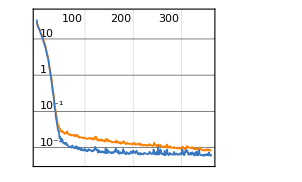
NetTrainResultsObject[NetTrain Results
summary | ,,  batches:3620  rounds:362  time:29s  examples/s:131755
data | ,,  training examples:10000  validation examples:5000  processed examples:3706880  skipped examples:0
method | ,,  ADAMoptimizer  batch size1024CPU
round | ,,  loss:8.26×10^-3
validation | ,,  loss:6.51×10^-3
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | ]

θ: {5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5}

θ̂: {5.00191,4.87608,4.87931,5.01141,4.9922,4.90825,5.00075,4.97371,5.04255,5.01938,5.13553,5.01745,4.98423,4.94028,4.99128,5.11681,5.04137,5.04782,4.98345,4.9081,4.96282,4.98675,5.04382,5.09397,5.01,4.93598,5.10156,5.06744,4.87176,4.95605,5.08321,4.99079,4.97359,4.91755,4.91579,4.91657,4.99625,4.96755,5.04473,4.98287,4.92763,4.93698,5.09142,4.99524,4.97265,4.82126,4.9836,5.10895,4.94905,5.00944,5.12064,4.94916,5.15828,5.01988,5.04821,5.00977,4.9939,5.02786,5.09286,5.04869,5.10356,5.01751,4.99543,4.97126,5.05371,4.99012,4.94015,4.88568,5.06423,4.9016,4.97918,5.06109,4.92616,4.91478,5.07658,5.11016,5.02612,4.97253,4.88842,4.99988,5.01986,5.00541,5.04293,4.90492,4.98566,5.17505,4.96799,5.01454,4.95751,4.96468,5.03075,5.07809,4.95133,4.9997,4.97385,4.97964,4.97892,5.04657,4.97188,4.85555}

abs(θ-θ̂): {0.00190687,0.123916,0.120694,0.0114083,0.00779772,0.0917511,0.000745296,0.0262909,0.0425539,0.0193777,0.135529,0.0174513,0.0157681,0.0597196,0.00871992,0.116807,0.0413666,0.0478163,0.0165539,0.091898,0.0371766,0.0132461,0.0438218,0.0939665,0.010005,0.0640178,0.101558,0.0674405,0.12824,0.0439472,0.0832062,0.00921345,0.0264053,0.082449,0.0842094,0.0834265,0.00375223,0.0324459,0.0447316,0.0171294,0.0723658,0.0630226,0.0914192,0.00476408,0.0273476,0.17874,0.0163984,0.108946,0.0509472,0.00944233,0.120636,0.0508385,0.158283,0.0198793,0.0482097,0.00977182,0.00610065,0.0278602,0.0928607,0.0486937,0.103563,0.0175099,0.00456715,0.0287385,0.0537124,0.0098834,0.0598521,0.114315,0.0642262,0.0983987,0.0208192,0.0610852,0.0738378,0.085218,0.0765753,0.11016,0.0261188,0.0274687,0.111583,0.000120163,0.0198641,0.00541067,0.0429335,0.0950837,0.0143414,0.175052,0.0320067,0.0145435,0.0424886,0.035316,0.0307531,0.0780921,0.048666,0.00029707,0.0261531,0.020359,0.0210786,0.0465722,0.0281186,0.144448}

Variance for θ:0.0046855

crb for θ:5/1024

ratio of variance and crb for θ:0.959591

RMSE:0.0685003

```mathematica
{Θ, e} = RunExperiment[PoissonDistribution, {1,10},5];
```

### Geometric distribution

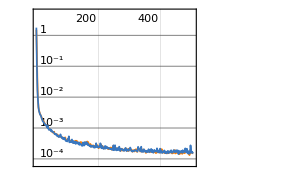
NetTrainResultsObject[NetTrain Results
summary | ,,  batches:5050  rounds:505  time:50s  examples/s:103993
data | ,,  training examples:10000  validation examples:5000  processed examples:5171200  skipped examples:0
method | ,,  ADAMoptimizer  batch size1024CPU
round | ,,  loss:1.52×10^-4
validation | ,,  loss:1.5×10^-4
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | ]

θ: {0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5}

θ̂: {0.528129,0.515687,0.503728,0.519624,0.494968,0.509834,0.499822,0.49979,0.502934,0.49251,0.489425,0.497049,0.502364,0.487538,0.51715,0.509424,0.485792,0.483656,0.503493,0.517123,0.496795,0.503305,0.512871,0.52341,0.51104,0.525332,0.482789,0.505203,0.506144,0.517749,0.519439,0.513743,0.513079,0.509345,0.533971,0.508186,0.505194,0.500039,0.482765,0.486379,0.524559,0.495977,0.493603,0.513604,0.501597,0.495787,0.508281,0.490378,0.508461,0.494756,0.502531,0.49086,0.489761,0.477024,0.513034,0.486879,0.510624,0.503129,0.50598,0.501353,0.516789,0.499779,0.529844,0.504031,0.505557,0.495822,0.504401,0.514986,0.493321,0.498785,0.491612,0.498149,0.506308,0.524597,0.505295,0.503557,0.517501,0.517985,0.487881,0.51268,0.497845,0.491548,0.504915,0.526108,0.509724,0.519116,0.505882,0.508381,0.518688,0.517531,0.509084,0.525161,0.517011,0.518106,0.518326,0.507021,0.493371,0.505733,0.50945,0.507537}

abs(θ-θ̂): {0.0281293,0.0156873,0.00372756,0.0196244,0.00503212,0.00983441,0.00017792,0.000209987,0.00293398,0.00749034,0.010575,0.00295085,0.00236416,0.0124621,0.0171501,0.00942421,0.0142078,0.0163435,0.00349319,0.0171229,0.0032053,0.00330484,0.0128708,0.02341,0.0110399,0.0253322,0.0172108,0.00520325,0.00614369,0.0177492,0.0194391,0.0137427,0.0130791,0.00934523,0.033971,0.00818604,0.00519425,0.0000385046,0.0172352,0.0136207,0.024559,0.00402299,0.00639668,0.0136044,0.00159723,0.00421301,0.00828081,0.00962228,0.00846124,0.00524384,0.00253081,0.00913978,0.0102389,0.0229757,0.0130343,0.0131206,0.0106236,0.00312912,0.00597996,0.00135279,0.0167886,0.000220954,0.0298437,0.00403118,0.00555706,0.00417849,0.00440079,0.0149863,0.00667858,0.00121504,0.00838766,0.00185117,0.00630796,0.0245971,0.00529468,0.00355744,0.0175013,0.017985,0.0121185,0.0126802,0.00215462,0.00845176,0.00491548,0.026108,0.00972414,0.0191161,0.00588232,0.00838053,0.0186884,0.0175307,0.00908393,0.0251613,0.0170114,0.0181056,0.018326,0.00702119,0.00662854,0.00573337,0.00945008,0.00753707}

Variance for θ:0.00017311

crb for θ:0.00012207

ratio of variance and crb for θ:1.41812

RMSE:0.0131571

```mathematica
{Θ, e} = RunExperiment[GeometricDistribution, {0.2,0.8},0.5];
```